# Dynamics of an Interaction between a Vacuum and Pressure-less Dark Matter

## Vacuum Interaction

## Q = q(x - ℛ)(1 - x)

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

### 2-D System

```mathematica
(*System of differential equations for x and z -> time variable is lna*)
dex:=x'=-3*q*(x-ℛ)*(1-x)
dez:=z'=-3*z+q*(x-ℛ)*(1-x)
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex==0,dez==0},{x,z}]
```

{{x→1,z→0},{x→ℛ,z→0}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],z/.FPs[[2,2]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,2}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dex,x],D[dex,z]}, {D[dez,x],D[dez,z]}}];
J//MatrixForm
```

(3 q (-1+2 x-ℛ) | 0
q (1-2 x+ℛ) | -3)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(1
0) | (-3 q (-1+ℛ) | 0
q (-1+ℛ) | -3) | (-3
-3 q (-1+ℛ)) | (0 | 1
-(3 (-1-q+q ℛ))/(q (-1+ℛ)) | 1)
(ℛ
0) | (3 q (-1+ℛ) | 0
q-q ℛ | -3) | (-3
3 q (-1+ℛ)) | (0 | 1
-(3 (1-q+q ℛ))/(q (-1+ℛ)) | 1)

```mathematica
Eqx[q_,ℛ_]=dex;
Eqz[q_,ℛ_]=dez;
```

```mathematica
Manipulate[StreamPlot[{Eqz[q,ℛ],Eqx[q,ℛ]},{z,-.2,1},{x,ℛ,1},FrameLabel->{"z","x"}],{q,0,1,Appearance->"Open"},{ℛ,0,1,Appearance->"Open"}]
```

### Compact 2-D System

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
dex:=x'=-3*q*(x-ℛ)*(1-x)
deZ:=Z'=-3*Z*(1-Z)+q*(1-Z)^2*(x-ℛ)*(1-x)
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex==0,deZ==0},{x,Z}]
```

{{x→1,Z→0},{x→ℛ,Z→0},{x→ℛ,Z→1},{x→1,Z→1}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x/.FPs[[1,1]],Z/.FPs[[1,2]]};
{{FP[2]={x/.FPs[[2,1]],Z/.FPs[[2,2]]};}, {FP[3]={x/.FPs[[3,1]],Z/.FPs[[3,2]]};
FP[4]={x/.FPs[[4,1]],Z/.FPs[[4,2]]};}}
```

{{Null},{Null^2}}

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,4}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dex,x],D[dex,Z]}, {D[deZ,x],D[deZ,Z]}}];
J//MatrixForm
```

(3 q (-1+2 x-ℛ) | 0
q (-1+Z)^2 (1-2 x+ℛ) | -3+6 Z-2 q (-1+x) (-1+Z) (x-ℛ))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],Z->FPs[[i,2]]}]//MatrixForm},{i,1,4}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(1
0) | (-3 q (-1+ℛ) | 0
q (-1+Z)^2 (-1+ℛ) | -3+6 Z) | (3 (-1+2 Z)
-3 q (-1+ℛ)) | (0 | 1
-(3 (-1-q+2 Z+q ℛ))/(q (-1+Z)^2 (-1+ℛ)) | 1)
(ℛ
0) | (3 q (-1+ℛ) | 0
-q (-1+Z)^2 (-1+ℛ) | -3+6 Z) | (3 (-1+2 Z)
3 q (-1+ℛ)) | (0 | 1
-(3 (1-q-2 Z+q ℛ))/(q (-1+Z)^2 (-1+ℛ)) | 1)
(ℛ
1) | (3 q (-1+ℛ) | 0
-q (-1+Z)^2 (-1+ℛ) | -3+6 Z) | (3 (-1+2 Z)
3 q (-1+ℛ)) | (0 | 1
-(3 (1-q-2 Z+q ℛ))/(q (-1+Z)^2 (-1+ℛ)) | 1)
(1
1) | (-3 q (-1+ℛ) | 0
q (-1+Z)^2 (-1+ℛ) | -3+6 Z) | (3 (-1+2 Z)
-3 q (-1+ℛ)) | (0 | 1
-(3 (-1-q+2 Z+q ℛ))/(q (-1+Z)^2 (-1+ℛ)) | 1)

```mathematica
Eqx[q_,ℛ_]=dex;
EqZ[q_,ℛ_]=deZ;
```

```mathematica
Manipulate[StreamPlot[{EqZ[q,ℛ],Eqx[q,ℛ]},{Z,0,1},{x,0,1},AxesLabel->{"Z","x"}],{q,0,1,Appearance->"Open"},{ℛ,0,1,Appearance->"Open"}]
```

### 3-D System

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*System of dimensionless differential equations*)
(*Dark energy, x, Hubble expansion, y, dark matter, z*)
de1:=x'=-3*y*q*(x-ℛ)*(1-x)
de2:=y'=-y^2-(1/6)*(z-2*x)
de3:=z'=-3*y*z+q*(x-ℛ)*(1-x)*y
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0},{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0,z→2 x},{x→1,y→-1/(√3),z→0},{x→1,y→1/(√3),z→0},{x→ℛ,y→-(√ℛ)/(√3),z→0},{x→ℛ,y→(√ℛ)/(√3),z→0}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,5}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z]}, {D[de2,x],D[de2,y],D[de2,z]},{D[de3,x],D[de3,y],D[de3,z]}}];
J//MatrixForm
```

(3 q y (-1+2 x-ℛ) | 3 q (-1+x) (x-ℛ) | 0
1/3 | -2 y | -1/6
q y (1-2 x+ℛ) | -3 z-q (-1+x) (x-ℛ) | -3 y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm},{i,1,5}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0
2 x) | (0 | 3 q (-1+x) (x-ℛ) | 0
1/3 | 0 | -1/6
0 | -6 x-q (-1+x) (x-ℛ) | 0) | (0
-(√(6 x-7 q x+7 q x^2+7 q ℛ-7 q x ℛ))/(√6)
(√(6 x-7 q x+7 q x^2+7 q ℛ-7 q x ℛ))/(√6)) | (1/2 | 0 | 1
-(3 (-q x+q x^2+q ℛ-q x ℛ))/(6 x-q x+q x^2+q ℛ-q x ℛ) | (√(6 x-7 q x+7 q x^2+7 q ℛ-7 q x ℛ))/(√6 (6 x-q x+q x^2+q ℛ-q x ℛ)) | 1
-(3 (-q x+q x^2+q ℛ-q x ℛ))/(6 x-q x+q x^2+q ℛ-q x ℛ) | -(√(6 x-7 q x+7 q x^2+7 q ℛ-7 q x ℛ))/(√6 (6 x-q x+q x^2+q ℛ-q x ℛ)) | 1)
(1
-1/(√3)
0) | (√3 q (-1+ℛ) | 0 | 0
1/3 | 2/(√3) | -1/6
-(q (-1+ℛ))/(√3) | 0 | √3) | (√3
2/(√3)
√3 q (-1+ℛ)) | (0 | -1/(2 √3) | 1
0 | 1 | 0
-(3 (-1-q+q ℛ))/(q (-1+ℛ)) | -(-6-7 q+7 q ℛ)/(2 √3 q (-1+ℛ) (-2-3 q+3 q ℛ)) | 1)
(1
1/(√3)
0) | (-√3 q (-1+ℛ) | 0 | 0
1/3 | -2/(√3) | -1/6
(q (-1+ℛ))/(√3) | 0 | -√3) | (-√3
-2/(√3)
-√3 q (-1+ℛ)) | (0 | 1/(2 √3) | 1
0 | 1 | 0
-(3 (-1-q+q ℛ))/(q (-1+ℛ)) | (-6-7 q+7 q ℛ)/(2 √3 q (-1+ℛ) (-2-3 q+3 q ℛ)) | 1)
(ℛ
-(√ℛ)/(√3)
0) | (-√3 q (-1+ℛ) √ℛ | 0 | 0
1/3 | (2 √ℛ)/(√3) | -1/6
(q (-1+ℛ) √ℛ)/(√3) | 0 | √3 √ℛ) | ((2 √ℛ)/(√3)
√3 √ℛ
-√3 q (-1+ℛ) √ℛ) | (0 | 1 | 0
0 | -1/(2 √3 √ℛ) | 1
-(3 (1-q+q ℛ))/(q (-1+ℛ)) | (6-7 q+7 q ℛ)/(2 √3 q (-1+ℛ) √ℛ (2-3 q+3 q ℛ)) | 1)
(ℛ
(√ℛ)/(√3)
0) | (√3 q (-1+ℛ) √ℛ | 0 | 0
1/3 | -(2 √ℛ)/(√3) | -1/6
-(q (-1+ℛ) √ℛ)/(√3) | 0 | -√3 √ℛ) | (-√3 √ℛ
-(2 √ℛ)/(√3)
√3 q (-1+ℛ) √ℛ) | (0 | 1/(2 √3 √ℛ) | 1
0 | 1 | 0
-(3 (1-q+q ℛ))/(q (-1+ℛ)) | -(6-7 q+7 q ℛ)/(2 √3 q (-1+ℛ) √ℛ (2-3 q+3 q ℛ)) | 1)

```mathematica
Eq1[q_,ℛ_]=de1;
Eq2[ℛ_]=de2;
Eq3[q_,ℛ_]=de3;
```

```mathematica
Manipulate[StreamPlot3D[{Eq1[q,ℛ],Eq2[ℛ],Eq3[q,ℛ]},{x,0,1},{y,-1,1},{z,0,10},AxesLabel->{"x","y","z"}],{q,0,5,Appearance->"Open"},{ℛ,0,1,Appearance->"Open"}]
```

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$30148'[System`VectorPlotsDump`t$30148]=={Eq1[0.5,0.1],Eq2[0.1],Eq3[0.5,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$30148[0]=={0.1,-0.8,1.,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$30148'[System`VectorPlotsDump`t$30148]=={Eq1[0.5,0.1],Eq2[0.1],Eq3[0.5,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$30148[0]=={0.1,-0.8,1.,0.},WhenEvent[«1»,StopIntegration]},«3»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$30148,System`VectorPlotsDump`linesxmax$30148},{System`VectorPlotsDump`linesymin$30148,System`VectorPlotsDump`linesymax$30148},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$30148,System`VectorPlotsDump`linesfieldmax$30148}} and System`VectorPlotsDump`extremes$30237 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$30148'[System`VectorPlotsDump`t$30148]=={Eq1[0.5,0.1],Eq2[0.1],Eq3[0.5,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$30148[0]=={0.1,-0.8,3.66667,0.},WhenEvent[«1»,StopIntegration]},«4»] and NDSolveValue[{System`VectorPlotsDump`w$30148'[System`VectorPlotsDump`t$30148]=={Eq1[0.5,0.1],Eq2[0.1],Eq3[0.5,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$30148[0]=={0.1,-0.8,3.66667,0.},WhenEvent[«1»,StopIntegration]},«4»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$30148,System`VectorPlotsDump`linesxmax$30148},{System`VectorPlotsDump`linesymin$30148,System`VectorPlotsDump`linesymax$30148},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$30148,System`VectorPlotsDump`linesfieldmax$30148}} and System`VectorPlotsDump`extremes$30319 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$30148,System`VectorPlotsDump`linesxmax$30148},{System`VectorPlotsDump`linesymin$30148,System`VectorPlotsDump`linesymax$30148},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$30148,System`VectorPlotsDump`linesfieldmax$30148}} and System`VectorPlotsDump`extremes$30393 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$18492,System`VectorPlotsDump`linesxmax$18492},{System`VectorPlotsDump`linesymin$18492,System`VectorPlotsDump`linesymax$18492},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$18492,System`VectorPlotsDump`linesfieldmax$18492}} and System`VectorPlotsDump`extremes$18579 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$18492,System`VectorPlotsDump`linesxmax$18492},{System`VectorPlotsDump`linesymin$18492,System`VectorPlotsDump`linesymax$18492},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$18492,System`VectorPlotsDump`linesfieldmax$18492}} and System`VectorPlotsDump`extremes$18663 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$18492,System`VectorPlotsDump`linesxmax$18492},{System`VectorPlotsDump`linesymin$18492,System`VectorPlotsDump`linesymax$18492},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$18492,System`VectorPlotsDump`linesfieldmax$18492}} and System`VectorPlotsDump`extremes$18741 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$20085,System`VectorPlotsDump`linesxmax$20085},{System`VectorPlotsDump`linesymin$20085,System`VectorPlotsDump`linesymax$20085},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$20085,System`VectorPlotsDump`linesfieldmax$20085}} and System`VectorPlotsDump`extremes$20145 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$20085,System`VectorPlotsDump`linesxmax$20085},{System`VectorPlotsDump`linesymin$20085,System`VectorPlotsDump`linesymax$20085},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$20085,System`VectorPlotsDump`linesfieldmax$20085}} and System`VectorPlotsDump`extremes$20213 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[«1»] and NDSolveValue[«1»] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$20085,System`VectorPlotsDump`linesxmax$20085},{System`VectorPlotsDump`linesymin$20085,System`VectorPlotsDump`linesymax$20085},{«38»,«38»},{System`VectorPlotsDump`linesfieldmin$20085,System`VectorPlotsDump`linesfieldmax$20085}} and System`VectorPlotsDump`extremes$20291 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads «1» and «1» at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$4278,System`VectorPlotsDump`linesxmax$4278},{System`VectorPlotsDump`linesymin$4278,System`VectorPlotsDump`linesymax$4278},{System`VectorPlotsDump`lineszmin$4278,«37»},{System`VectorPlotsDump`linesfieldmin$4278,System`VectorPlotsDump`linesfieldmax$4278}} and System`VectorPlotsDump`extremes$4395 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$4278'[System`VectorPlotsDump`t$4278]=={Eq1[0.5,0.1],Eq2[0.1],Eq3[0.5,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$4278[0]=={0.1,-0.8,3.66667,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Extr…dler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$4278'[System`VectorPlotsDump`t$4278]=={Eq1[0.5,0.1],Eq2[0.1],Eq3[0.5,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$4278[0]=={0.1,-0.8,3.66667,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Extr…dler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$4278,System`VectorPlotsDump`linesxmax$4278},{System`VectorPlotsDump`linesymin$4278,System`VectorPlotsDump`linesymax$4278},{System`VectorPlotsDump`lineszmin$4278,«37»},{System`VectorPlotsDump`linesfieldmin$4278,System`VectorPlotsDump`linesfieldmax$4278}} and System`VectorPlotsDump`extremes$4490 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$4278'[System`VectorPlotsDump`t$4278]=={Eq1[0.5,0.1],Eq2[0.1],Eq3[0.5,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$4278[0]=={0.1,-0.8,6.33333,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Extr…ndler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$4278'[System`VectorPlotsDump`t$4278]=={Eq1[0.5,0.1],Eq2[0.1],Eq3[0.5,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$4278[0]=={0.1,-0.8,6.33333,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Extr…ndler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$4278,System`VectorPlotsDump`linesxmax$4278},{System`VectorPlotsDump`linesymin$4278,System`VectorPlotsDump`linesymax$4278},{System`VectorPlotsDump`lineszmin$4278,«37»},{System`VectorPlotsDump`linesfieldmin$4278,System`VectorPlotsDump`linesfieldmax$4278}} and System`VectorPlotsDump`extremes$4578 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads «1» and «1» at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$7432,System`VectorPlotsDump`linesxmax$7432},{System`VectorPlotsDump`linesymin$7432,System`VectorPlotsDump`linesymax$7432},{System`VectorPlotsDump`lineszmin$7432,«37»},{System`VectorPlotsDump`linesfieldmin$7432,System`VectorPlotsDump`linesfieldmax$7432}} and System`VectorPlotsDump`extremes$7498 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$7432'[System`VectorPlotsDump`t$7432]=={Eq1[0.5,0.1],Eq2[0.1],Eq3[0.5,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$7432[0]=={0.1,-0.8,3.66667,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Extr…dler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$7432'[System`VectorPlotsDump`t$7432]=={Eq1[0.5,0.1],Eq2[0.1],Eq3[0.5,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$7432[0]=={0.1,-0.8,3.66667,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Extr…dler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$7432,System`VectorPlotsDump`linesxmax$7432},{System`VectorPlotsDump`linesymin$7432,System`VectorPlotsDump`linesymax$7432},{System`VectorPlotsDump`lineszmin$7432,«37»},{System`VectorPlotsDump`linesfieldmin$7432,System`VectorPlotsDump`linesfieldmax$7432}} and System`VectorPlotsDump`extremes$7572 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$7432'[System`VectorPlotsDump`t$7432]=={Eq1[0.5,0.1],Eq2[0.1],Eq3[0.5,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$7432[0]=={0.1,-0.8,6.33333,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Extr…ndler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$7432'[System`VectorPlotsDump`t$7432]=={Eq1[0.5,0.1],Eq2[0.1],Eq3[0.5,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$7432[0]=={0.1,-0.8,6.33333,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Extr…ndler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$7432,System`VectorPlotsDump`linesxmax$7432},{System`VectorPlotsDump`linesymin$7432,System`VectorPlotsDump`linesymax$7432},{System`VectorPlotsDump`lineszmin$7432,«37»},{System`VectorPlotsDump`linesfieldmin$7432,System`VectorPlotsDump`linesfieldmax$7432}} and System`VectorPlotsDump`extremes$7652 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads «1» and «1» at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Part::partw: Part 4 of Interpolation[{Null,{}}⟦2,1⟧] does not exist.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$5682,System`VectorPlotsDump`linesxmax$5682},{System`VectorPlotsDump`linesymin$5682,System`VectorPlotsDump`linesymax$5682},{System`VectorPlotsDump`lineszmin$5682,«37»},{System`VectorPlotsDump`linesfieldmin$5682,System`VectorPlotsDump`linesfieldmax$5682}} and System`VectorPlotsDump`extremes$5801 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$5682'[System`VectorPlotsDump`t$5682]=={Eq1[0.5,0.1],Eq2[0.1],Eq3[0.5,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$5682[0]=={0.1,-0.8,3.66667,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Extr…dler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$5682'[System`VectorPlotsDump`t$5682]=={Eq1[0.5,0.1],Eq2[0.1],Eq3[0.5,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$5682[0]=={0.1,-0.8,3.66667,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Extr…dler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$5682,System`VectorPlotsDump`linesxmax$5682},{System`VectorPlotsDump`linesymin$5682,System`VectorPlotsDump`linesymax$5682},{System`VectorPlotsDump`lineszmin$5682,«37»},{System`VectorPlotsDump`linesfieldmin$5682,System`VectorPlotsDump`linesfieldmax$5682}} and System`VectorPlotsDump`extremes$5905 are not the same shape.

Rest::normal: Nonatomic expression expected at position 1 in Rest[Coordinates].

General::stop: Further output of Rest::normal will be suppressed during this calculation.

Join::heads: Heads NDSolveValue[{System`VectorPlotsDump`w$5682'[System`VectorPlotsDump`t$5682]=={Eq1[0.5,0.1],Eq2[0.1],Eq3[0.5,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$5682[0]=={0.1,-0.8,6.33333,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Extr…ndler→«1»,Method→Automatic] and NDSolveValue[{System`VectorPlotsDump`w$5682'[System`VectorPlotsDump`t$5682]=={Eq1[0.5,0.1],Eq2[0.1],Eq3[0.5,0.1],√(Eq1[«2»]^2+Eq2[«1»]^2+Eq3[«2»]^2)},System`VectorPlotsDump`w$5682[0]=={0.1,-0.8,6.33333,0.},WhenEvent[«1»,StopIntegration]},«29»,«1»,Extr…ndler→«1»,Method→Automatic] at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Interpolation::innd: First argument in {Null,{}}⟦2,1⟧ does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

PropertyValue::pvobj: Interpolation[{Null,{}}⟦2,1⟧] is not an object with properties.

General::stop: Further output of PropertyValue::pvobj will be suppressed during this calculation.

Set::shape: Lists {{System`VectorPlotsDump`linesxmin$5682,System`VectorPlotsDump`linesxmax$5682},{System`VectorPlotsDump`linesymin$5682,System`VectorPlotsDump`linesymax$5682},{System`VectorPlotsDump`lineszmin$5682,«37»},{System`VectorPlotsDump`linesfieldmin$5682,System`VectorPlotsDump`linesfieldmax$5682}} and System`VectorPlotsDump`extremes$5995 are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

### Numeric Compact Phase Plot

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
de1t:=x1'[t]==-3*Y[t]*q*(x1[t]-ℛ)*(1-x1[t])/((1-Y[t]^2)^(1/2))
de2t:=Y'[t]==-(Y[t]^2)*(1-Y[t]^2)^(1/2)-(((1-Y[t]^2)^(3/2))/6)*((Z[t]/(1-Z[t]))-2*x1[t])
de3t:=Z'[t]==-3*Y[t]*Z[t]*(1-Z[t])/((1-Y[t]^2)^(1/2))+q*(1-Z[t])^2*(x1[t]-ℛ)*(1-x1[t])*Y[t]/((1-Y[t]^2)^(1/2))
```

```mathematica
q=1;
ℛ=0.01;
```

```mathematica
traj[x0_,Y0_,Z0_]=NDSolve[{de1t,de2t,de3t, x1[0]==x0,Y[0]==Y0,Z[0]==Z0}, {x1,Y,Z},{t,-1000,1000}];
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

```mathematica
sol[1]=traj[0.2,0.01,0.009];
sol[2]=traj[0.2,0.05,0.009];
sol[3]=traj[0.2,0.1,0.009];
sol[4]=traj[0.2,0.15,0.009];
sol[5]=traj[0.2,0.2,0.009];
sol[6]=traj[0.2,0.25,0.009];
sol[7]=traj[0.2,0.3,0.009];
sol[8]=traj[1,0.33,0.009];
```

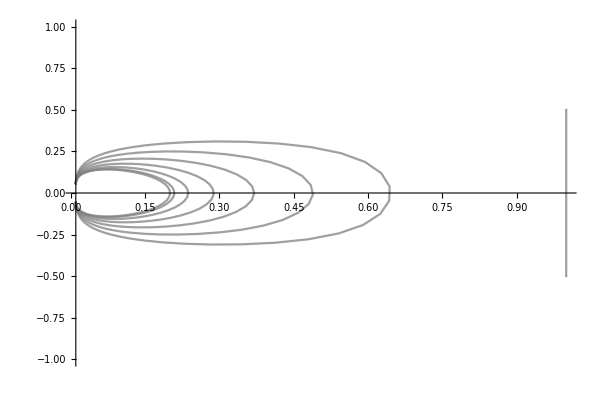

```mathematica
ParametricPlot[Evaluate[Table[{x1[t],Y[t]}/.sol[i],{i,1,8}], {t,-500,500},PlotStyle -> {{Gray, Opacity[0.75]}},ImageSize->{600,400},PlotRange->{{ℛ,1},{-1,1}}]]
```

```mathematica
(*Define the scale factor (a) as a function of x*)
ca[x0_]=(1-x0)/(x0-ℛ);
a[x_,x0_]=(ca[x0]*((x-ℛ)/(1-x)))^((-1)/(3*q*(1-ℛ)));
```

Power::infy: Infinite expression 1/0.^0.0673401 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

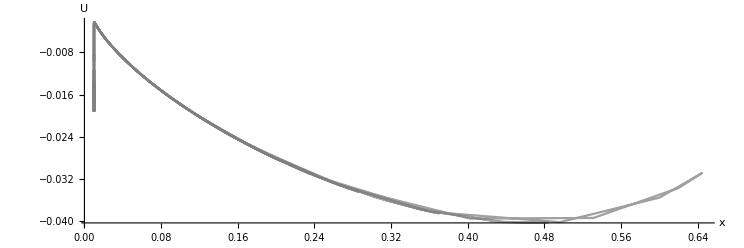

```mathematica
(*Plot the potential (U) against x*)
Potential=ParametricPlot[Evaluate[Table[{x1[t],-(a[x1[t],0.02]/6)*(x1[t]+Z[t]/(1-Z[t]))}/.sol[i],{i,1,7}], {t,-1000,1000},PlotStyle -> {{Gray, Opacity[0.75]}},ImageSize->{600,200}],PlotRange->All,AxesLabel->{"x","U"}]
```

```mathematica
(*Define the energy of the trajectories*)
Energy[x0_,y0_,z0_]=-(x0/6+z0/6-y0^2/2);
```

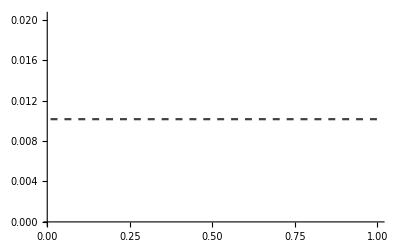

```mathematica
(*Plot the energy of the trajectories*)
TrajE=Plot[{Energy[0.2,0.3,0.009]},{x,ℛ,1},PlotStyle->{Black,Dashed,Opacity[0.75]}]
```

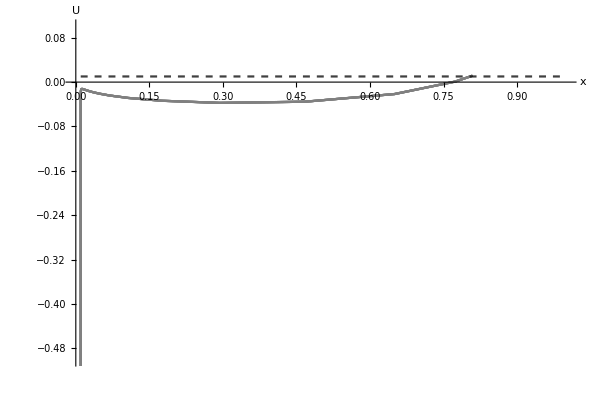

```mathematica
(*Show the potential and energy of the trajectories*)
Show[Potential,TrajE]
```